```mathematica
w1[θ_,r_]:=Sin[θ-ArcTan[((√3)/2-Sin[θ])/(r-1-Cos[θ])]]
```

```mathematica
w2[θ_,r_]:=Sin[θ+ArcTan[Sin[θ]/(r-1-Cos[θ])]]
```

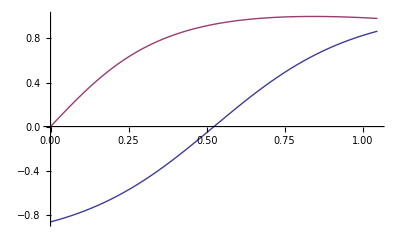

```mathematica
Plot[{w1[θ,2.5],w2[θ,2.5]},{θ,0,π/3}]
```

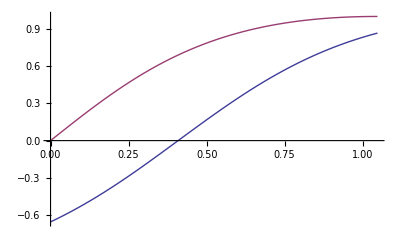

```mathematica
Plot[{w1[θ,3],w2[θ,3]},{θ,0,π/3}]
```

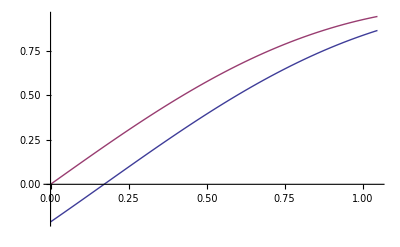

```mathematica
Plot[{w1[θ,6],w2[θ,6]},{θ,0,π/3}]
```

```mathematica
FullSimplify[D[w2[θ,r],θ]]
```

```mathematica
w2prime[θ_,r_]:=((-1+r) (-1+r-Cos[θ]) Cos[θ+ArcCot[(-1+r-Cos[θ]) Csc[θ]]])/(2+(-2+r) r-2 (-1+r) Cos[θ])
```

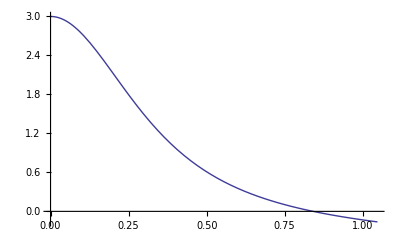

```mathematica
Plot[w2prime[θ,2.5],{θ,0,π/3}]
```

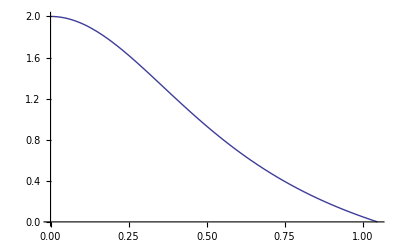

```mathematica
Plot[w2prime[θ,3],{θ,0,π/3}]
```

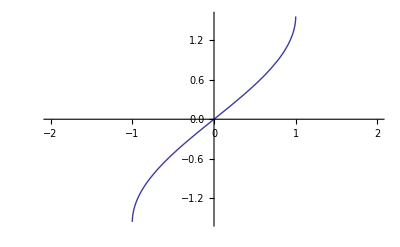

```mathematica
Plot[ArcSin[x],{x,-2,2}]
```

```mathematica
(***************)
```

```mathematica
α[n_,m_]:=Which[n==1&&m==2,0,n==2&&m==3,(2π)/3,n==3&&m==1,(4π)/3,n==2&&m==1,π,n==3&&m==2,(5π)/3,n==1&&m==3,π/3]
```

```mathematica
α[3,2]
```

(5 π)/3

```mathematica
wnext[w_,θ_,n_,m_,r_]:=w-r (w Cos[θ-α[n,m]]+√(1-w^2)Sin[θ-α[n,m]])
```

```mathematica
T[w_,θ_,n_,m_,r_]:={w-r (w Cos[θ-α[n,m]]+√(1-w^2)Sin[θ-α[n,m]]),Mod[θ+π+ArcSin[w] +ArcSin[wnext[w,θ,n,m,r]] ,2π]}
```

```mathematica
T[0.1,0.2,1,2,3]
```

-0.78704

```mathematica
T[-0.7870404381907682,2.5357633313989965,2,3,3]
```

{0.557232,5.36241}

```mathematica
T[0.5572317476793701,5.362407488061782,3,1,3]
```

{-2.38657,1.24107+1.5159 ⅈ}

```mathematica
f[w_,θ_]:=T[T[T[w,θ,1,2,3][[1]],T[w,θ,1,2,3][[2]],2,3,3][[1]],T[T[w,θ,1,2,3][[1]],T[w,θ,1,2,3][[2]],2,3,3][[2]],3,1,3]-{w,θ}
```

```mathematica
f[0.1,0.2]
```

{-2.48657,1.04107+1.5159 ⅈ}

```mathematica
FindRoot[{f[w,θ][[1]]==0,f[w,θ][[2]]==0},{w,-0.5},{θ,0.5}]
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function.  You may need more than MachinePrecision digits of working precision to meet these tolerances.

{w→-1.63017+0.471299 ⅈ,θ→0.82791-0.924178 ⅈ}

```mathematica
Plot3D[T[w,θ,1,2,3]-{w,θ},{w,-1,1},{θ,0,π/3}]
```

-Graphics3D-

```mathematica
Plot3D[T[T[w,θ,1,2,3][[1]],T[w,θ,1,2,3][[2]],2,3,3]-{w,θ},{w,-1,1},{θ,0,π/3}]
```

-Graphics3D-

```mathematica
Plot3D[T[T[T[w,θ,1,2,3][[1]],T[w,θ,1,2,3][[2]],2,3,3][[1]],T[T[w,θ,1,2,3][[1]],T[w,θ,1,2,3][[2]],2,3,3][[2]],3,1,3]-{w,θ},{w,-1,1},{θ,0,π/3}]
```

-Graphics3D-

```mathematica
Plot3D[f[w,θ]==0,{w,-1,1},{θ,0,π/3}]
```

-Graphics3D-

```mathematica
f[-0.5,π/6]
```

{-2.33147×10^-15,-2.33147×10^-15}

```mathematica
FullSimplify[T[Sin[ϕ],θ,n,m,r],ϕ>-π/2&&ϕ<π/2]
```

{Sin[ϕ]-r Sin[θ+ϕ-Which[n==1&&m==2,0,n==2&&m==3,(2 π)/3,n==3&&m==1,(4 π)/3,n==2&&m==1,π,n==3&&m==2,(5 π)/3,n==1&&m==3,π/3]],Mod[π+θ+ϕ+ArcSin[Sin[ϕ]-r Sin[θ+ϕ-Which[n==1&&m==2,0,n==2&&m==3,(2 π)/3,n==3&&m==1,(4 π)/3,n==2&&m==1,π,n==3&&m==2,(5 π)/3,n==1&&m==3,π/3]]],2 π]}

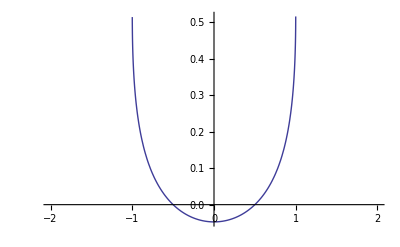

```mathematica
Plot[ArcSin[x]/x-π/3,{x,-2,2}]
```

```mathematica
T[-0.5,π/6,1,3,1]
```

{0.366025,3.51633}

```mathematica
T[0.3660254037844386,3.516327086298533,3,1,1]
```

{0.659375,1.46946}

```mathematica
f1[w_,θ_]:=T[T[w,θ,1,3,1][[1]],T[w,θ,1,3,1][[2]],3,1,1]-{w,θ}
```

```mathematica
f1[-0.5,π/6]
```

{1.15937,0.945857}

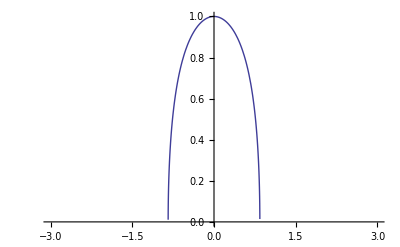

```mathematica
Plot[√(1-ArcSin[x]^2),{x,-3,3}]
```

```mathematica
Sin[1]//N
```

0.841471

```mathematica
Plot3D[√(1-x^2)ArcSin[y],{x,-2,2},{y,-2,2}]
```

-Graphics3D-

```mathematica
Plot3D[√(1-(x y)^2)ArcSin[y-x],{x,-2,2},{y,-2,2},AxesLabel->{"x","y","z"}]
```

-Graphics3D-

```mathematica
f4[x_,y_]:=√(1-(x y)^2)ArcSin[y-x]
```

```mathematica
f4[Interval[{0,1}],Interval[{-0.4,0.3}]]
```

ArcSin[Interval[{-1.4,0.3}]] Interval[{0.916515,1}]

```mathematica
Interval[{0,1}]-Interval[{-0.4,0.3}]
```

Interval[{-0.3,1.4}]

```mathematica
ArcSin[Interval[{-1.4000000000000004,0.3000000000000001}]] //N
```

ArcSin[Interval[{-1.4,0.3}]]

```mathematica
w1:=Interval[{-5.04187500000000000033*10^-01,-5.02249999999999999993*10^-01}]
```

```mathematica
θ1:=Interval[{5.19411275598298799959*10^-01,5.21348775598298800054*10^-01}]
```

```mathematica
T[w1,θ1,1,2,3]
```

{Interval[{-0.4896374651543408949,-0.4751615811322693207}],Mod[Interval[{2.6208891397604132938,2.6415949642549472745}],2 π]}

```mathematica
Plot3D[ArcSin[x-y],{x,-3,3},{y,-3,3}]
```

-Graphics3D-

```mathematica
Plot3D[√(x+y),{x,-3,3},{y,-3,3}]
```

-Graphics3D-

```mathematica
Interval[{-2,0},{1,4}]-Interval[{1,2}]
```

Interval[{-4,3}]

```mathematica
Interval[{-2,0},{1,4}]+Interval[{1,2}]
```

Interval[{-1,6}]

```mathematica
Interval[{-2,0}] - Interval[{1,2}]
```

Interval[{-4,-1}]

```mathematica
Interval[{1,4}] - Interval[{1,2}]
```

Interval[{-1,3}]

```mathematica
Interval[{-2,0},{1,4}]+Interval[{1,2},{5,7}]
```

Interval[{-1,11}]

```mathematica
Interval[{-2,0}]+Interval[{1,2}]
```

Interval[{-1,2}]

```mathematica
Interval[{-2,0}]+Interval[{5,7}]
```

Interval[{3,7}]

```mathematica
Interval[{1,4}]+Interval[{1,2}]
```

Interval[{2,6}]

```mathematica
Interval[{1,4}]+Interval[{5,7}]
```

Interval[{6,11}]

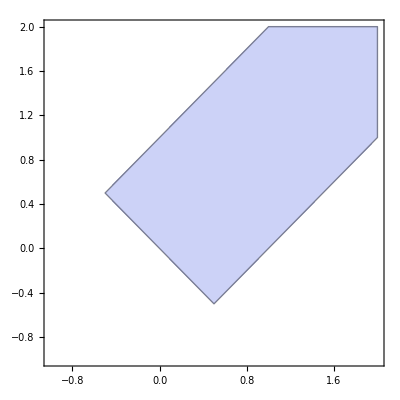

```mathematica
RegionPlot[Abs[x-y]≤1&&x+y>0,{x,-1,2},{y,-1,2}]
```